```mathematica
ПОИСК КРАТЧАЙШЕГО ПУТИ ВО ВЗВЕШЕННОМ ГРАФЕ. ЗАДАЧА КОММИВОЯЖЕРА
```

```mathematica
Граф, являющийся подграфом графа - решетки 8*8 (рис. 1), задан списками  ориетированных (Ded) и неориентированных ребер (Ued), с указанием веса (длины) ребра. Требуется, в соответствии с вариантом задания:
1.  Построить граф;
2.  Найти кратчайший путь от вершины v1 до вершины v2 и его длину ;
3.  Найти кратчайший замкнутый маршрут (маршрут коммивояжера) от вершины v1 через вершины v2,v3,v4 (в любой последовательности)и его SuperStar[длину] ;
4.  Отобразить найденные маршруты на графе.
```

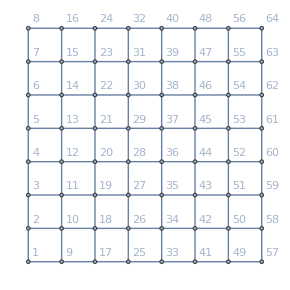
```mathematica
-Graphics-
Рис. 1. Неориентированный граф-решетка 8*8
```

```mathematica
Вариант 1
Ded={{25,17,2},{10,2,3},{26,18,5},{15,14,3},{50,42,1},{19,11,3},{23,22,4},{28,27,4},{28,20,4},{30,29,5},{1,9,3},{5,6,6},{11,12,4},{21,22,5},{12,20,3},{28,29,6},{30,31,2},{31,32,3},{47,48,2},{54,62,4},{31,39,4},{60,61,1}}
Ued={{1,2,2},{2,3,5},{9,17,4},{3,4,5},{4,5,4},{33,41,1},{7,8,2},{49,57,1},{9,10,3},{10,11,2},{10,18,2},{12,13,5},{26,34,3},{15,16,6},{50,58,6},{17,18,5},{3,11,6},{18,19,2},{19,20,6},{20,21,5},{27,35,3},{35,43,3},{43,51,5},{23,24,1},{25,26,1},{4,12,2},{26,27,6},{28,36,6},{36,44,6},{44,52,6},{52,60,5},{33,34,5},{13,21,1},{35,36,6},{21,29,2},{36,37,5},{37,38,4},{37,45,5},{38,39,1},{39,40,5},{53,61,5},{41,42,6},{6,14,1},{42,43,1},{14,22,2},{22,30,1},{44,45,4},{30,38,4},{45,46,3},{38,46,5},{46,47,2},{49,50,3},{50,51,6},{15,23,1},{23,31,5},{52,53,3},{53,54,5},{39,47,4},{54,55,5},{55,63,6},{57,58,3},{8,16,6},{16,24,6},{59,60,5},{24,32,6},{32,40,5},{61,62,3},{40,48,6},{62,63,1},{48,56,5},{63,64,4}}
{v1,v2,v3,v4}={1,64,22,52}
```

```mathematica
Вариант 2
Ded={{33,25,1},{8,7,2},{10,9,5},{10,2,5},{59,51,3},{58,57,4},{62,61,1},{1,2,5},{1,9,5},{2,3,3},{9,17,5},{4,5,4},{5,6,1},{11,12,3},{34,42,3},{3,11,4},{19,20,5},{35,43,5},{43,51,2},{12,20,5},{22,30,6},{47,48,2},{54,62,6},{16,24,5},{24,32,6},{32,40,2}}
Ued={{3,4,2},{17,25,2},{6,7,5},{41,49,2},{49,57,3},{26,34,1},{13,14,6},{14,15,1},{42,50,4},{15,16,4},{50,58,2},{17,18,1},{18,19,3},{11,19,4},{19,27,1},{27,35,1},{21,22,5},{22,23,6},{23,24,5},{26,27,4},{27,28,5},{20,28,1},{28,36,1},{36,44,3},{30,31,6},{31,32,1},{52,60,1},{33,34,4},{34,35,4},{13,21,3},{35,36,5},{21,29,1},{29,37,1},{37,38,1},{37,45,2},{38,39,4},{45,53,6},{39,40,5},{53,61,4},{41,42,2},{6,14,1},{42,43,3},{14,22,3},{43,44,3},{44,45,5},{45,46,1},{46,47,1},{7,15,2},{50,51,6},{15,23,6},{51,52,2},{23,31,2},{52,53,6},{31,39,6},{53,54,5},{39,47,1},{54,55,4},{47,55,4},{55,63,6},{8,16,1},{58,59,1},{59,60,6},{60,61,4},{62,63,6},{48,56,4},{63,64,3},{56,64,3}}
{v1,v2,v3,v4}={1,56,15,51}
```

```mathematica
Вариант 3
Ded={{13,12,2},{22,21,5},{27,26,3},{13,5,5},{35,34,2},{36,35,3},{37,36,3},{45,37,6},{56,48,1},{3,4,4},{6,7,2},{17,18,3},{12,20,2},{36,44,5},{33,34,2},{13,21,5},{44,45,1},{46,54,1},{50,51,3},{32,40,6},{61,62,3}}
Ued={{1,9,6},{2,3,3},{9,17,3},{17,25,1},{4,5,6},{25,33,5},{5,6,1},{33,41,4},{41,49,1},{7,8,1},{49,57,3},{2,10,2},{10,11,5},{10,18,3},{11,12,6},{18,26,2},{26,34,2},{13,14,1},{34,42,1},{14,15,2},{42,50,3},{15,16,2},{18,19,3},{11,19,6},{19,20,1},{19,27,3},{20,21,4},{27,35,1},{35,43,2},{22,23,3},{43,51,2},{23,24,4},{25,26,4},{27,28,6},{20,28,2},{28,36,4},{29,30,1},{30,31,1},{44,52,3},{31,32,2},{52,60,3},{29,37,6},{37,38,5},{38,39,4},{45,53,2},{53,61,4},{41,42,3},{6,14,4},{42,43,4},{14,22,3},{22,30,5},{30,38,1},{54,62,5},{49,50,5},{7,15,1},{15,23,5},{51,52,6},{23,31,2},{52,53,3},{53,54,6},{39,47,2},{54,55,2},{55,56,2},{55,63,4},{57,58,6},{8,16,2},{58,59,3},{16,24,4},{59,60,2},{24,32,5},{60,61,5},{40,48,2},{56,64,4}}
{v1,v2,v3,v4}={7,57,48,34}
```

```mathematica
Вариант 4
Ded={{24,23,1},{30,29,3},{44,36,1},{21,13,2},{61,53,1},{47,46,5},{62,54,5},{52,51,1},{2,3,1},{3,4,5},{5,6,1},{41,49,4},{9,10,4},{12,20,1},{27,28,1},{30,31,1},{5,13,6},{37,38,3},{39,40,4},{22,30,1},{45,46,6},{31,39,2},{54,55,4},{55,63,4},{24,32,3}}
Ued={{1,2,4},{1,9,3},{9,17,1},{17,25,3},{4,5,2},{25,33,1},{33,41,3},{6,7,1},{7,8,4},{2,10,4},{10,11,6},{10,18,2},{11,12,2},{18,26,2},{12,13,5},{26,34,5},{13,14,5},{34,42,3},{14,15,2},{15,16,4},{50,58,5},{3,11,6},{19,20,5},{19,27,1},{20,21,4},{27,35,6},{21,22,1},{35,43,5},{22,23,4},{51,59,5},{25,26,1},{26,27,2},{20,28,1},{28,29,5},{28,36,5},{44,52,3},{31,32,2},{33,34,2},{34,35,2},{35,36,1},{21,29,1},{36,37,5},{29,37,2},{37,45,3},{42,43,1},{44,45,6},{30,38,2},{38,46,4},{46,54,3},{47,48,2},{49,50,1},{50,51,3},{15,23,5},{23,31,6},{52,53,4},{47,55,2},{55,56,4},{57,58,3},{8,16,3},{58,59,4},{16,24,5},{59,60,4},{60,61,2},{32,40,1},{61,62,1},{62,63,1},{48,56,2},{63,64,5},{56,64,3}}
{v1,v2,v3,v4}={1,55,48,34}
```

```mathematica
Вариант 5
Ded={{18,10,1},{13,12,4},{18,17,2},{24,23,2},{29,28,2},{14,6,4},{48,47,1},{63,55,5},{58,57,6},{24,16,4},{9,17,3},{49,57,2},{10,11,6},{3,11,4},{18,19,5},{35,43,5},{30,31,3},{31,32,1},{21,29,5},{44,45,5},{30,38,5},{38,46,4},{7,15,3},{31,39,4},{59,60,3},{60,61,4},{62,63,5}}
Ued={{1,9,6},{2,3,1},{17,25,1},{4,5,3},{25,33,2},{5,6,6},{33,41,1},{6,7,6},{41,49,2},{7,8,5},{9,10,6},{2,10,6},{11,12,2},{26,34,1},{13,14,3},{34,42,3},{14,15,6},{15,16,1},{50,58,4},{11,19,4},{19,20,3},{19,27,3},{20,21,6},{27,35,5},{22,23,6},{43,51,4},{25,26,1},{4,12,6},{12,20,5},{27,28,5},{20,28,2},{28,36,1},{29,30,1},{36,44,2},{44,52,5},{52,60,4},{33,34,3},{5,13,1},{34,35,4},{13,21,4},{36,37,3},{37,45,6},{38,39,6},{45,53,3},{39,40,4},{42,43,1},{14,22,1},{43,44,1},{45,46,4},{46,47,6},{46,54,3},{54,62,3},{50,51,4},{15,23,5},{51,52,3},{23,31,1},{52,53,3},{39,47,5},{54,55,3},{47,55,2},{55,56,1},{58,59,3},{24,32,3},{32,40,4},{61,62,1},{48,56,5},{63,64,6},{56,64,4}}
{v1,v2,v3,v4}={9,64,23,52}
```

```mathematica
Вариант 6
Ded={{11,10,2},{18,10,2},{23,22,1},{28,27,1},{36,28,6},{56,55,5},{40,32,2},{7,8,2},{15,16,4},{50,58,6},{3,11,4},{18,19,1},{11,19,6},{20,21,5},{4,12,2},{12,20,6},{5,13,6},{41,42,6},{14,22,2},{22,30,6},{46,47,1},{54,62,2},{49,50,3},{63,64,6}}
Ued={{1,2,4},{1,9,6},{2,3,5},{9,17,2},{3,4,4},{17,25,4},{4,5,5},{25,33,4},{5,6,1},{33,41,2},{6,7,6},{41,49,5},{49,57,6},{9,10,1},{2,10,4},{11,12,3},{12,13,5},{26,34,5},{13,14,4},{14,15,4},{42,50,1},{19,20,6},{19,27,5},{27,35,2},{21,22,4},{35,43,5},{43,51,2},{23,24,4},{51,59,1},{25,26,1},{20,28,3},{28,29,5},{29,30,1},{30,31,5},{44,52,1},{34,35,1},{13,21,2},{36,37,6},{29,37,6},{37,45,1},{38,39,2},{6,14,4},{42,43,2},{43,44,2},{44,45,5},{30,38,6},{46,54,3},{47,48,4},{7,15,6},{15,23,5},{51,52,5},{23,31,4},{52,53,6},{31,39,3},{53,54,3},{54,55,1},{47,55,5},{55,63,6},{57,58,1},{8,16,6},{58,59,2},{16,24,4},{59,60,5},{24,32,3},{61,62,5},{40,48,6},{62,63,5},{48,56,6},{56,64,2}}
{v1,v2,v3,v4}={1,54,8,58}
```

```mathematica
Вариант 7
Ded={{7,6,1},{59,51,5},{20,12,6},{37,36,5},{62,54,3},{52,51,5},{48,40,4},{64,56,6},{4,5,2},{26,34,6},{42,50,6},{20,21,1},{35,43,2},{23,24,1},{36,44,4},{35,36,3},{45,53,1},{39,40,2},{38,46,1},{31,39,5},{62,63,5}}
Ued={{1,2,1},{1,9,3},{2,3,1},{3,4,2},{25,33,6},{5,6,3},{33,41,6},{41,49,6},{7,8,4},{49,57,4},{9,10,5},{2,10,4},{10,11,6},{10,18,3},{18,26,2},{13,14,4},{34,42,6},{14,15,6},{50,58,2},{3,11,1},{18,19,2},{19,20,2},{27,35,6},{22,23,6},{43,51,1},{25,26,3},{4,12,4},{26,27,6},{20,28,5},{28,29,5},{28,36,4},{29,30,6},{30,31,3},{44,52,1},{52,60,2},{33,34,5},{5,13,1},{34,35,5},{21,29,2},{29,37,5},{37,38,6},{37,45,6},{38,39,3},{53,61,5},{6,14,4},{43,44,2},{22,30,5},{44,45,1},{30,38,6},{45,46,5},{46,47,5},{46,54,3},{49,50,4},{7,15,5},{50,51,1},{15,23,4},{23,31,2},{52,53,1},{53,54,3},{39,47,6},{54,55,2},{47,55,6},{55,56,1},{55,63,4},{57,58,6},{8,16,4},{58,59,2},{16,24,2},{59,60,5},{24,32,2},{60,61,1},{32,40,3},{48,56,6},{63,64,2}}
{v1,v2,v3,v4}={7,60,48,33}
```

```mathematica
Вариант 8
Ded={{16,15,2},{22,21,1},{27,26,5},{32,31,3},{60,52,4},{13,5,1},{42,41,3},{41,49,3},{10,18,3},{18,26,2},{13,14,5},{3,11,5},{18,19,6},{19,20,3},{44,52,3},{13,21,4},{29,37,5},{53,61,3},{45,46,4},{15,23,6},{55,56,4},{55,63,3},{17,18,2},{56,48,3}}
Ued={{1,2,6},{1,9,2},{2,3,2},{3,4,6},{17,25,3},{4,5,3},{5,6,2},{33,41,6},{7,8,2},{49,57,3},{9,10,6},{10,11,3},{11,12,2},{26,34,3},{34,42,2},{14,15,1},{42,50,2},{50,58,6},{11,19,1},{19,27,5},{27,35,3},{35,43,1},{22,23,1},{43,51,4},{23,24,6},{51,59,2},{25,26,4},{4,12,2},{12,20,6},{28,29,5},{29,30,4},{36,44,5},{30,31,1},{34,35,3},{35,36,2},{21,29,6},{36,37,5},{37,38,4},{37,45,2},{38,39,5},{39,40,5},{6,14,5},{42,43,5},{14,22,4},{43,44,3},{22,30,3},{44,45,2},{30,38,1},{38,46,1},{46,47,2},{46,54,6},{47,48,1},{54,62,2},{49,50,4},{7,15,6},{51,52,2},{23,31,5},{52,53,2},{31,39,3},{53,54,2},{39,47,4},{54,55,6},{47,55,6},{8,16,5},{58,59,2},{16,24,6},{59,60,1},{60,61,4},{32,40,4},{62,63,1},{63,64,5},{56,64,2}}
{v1,v2,v3,v4}={9,63,16,12}
```

```mathematica
Вариант 9
Ded={{12,4,4},{30,29,2},{45,44,3},{54,46,5},{53,52,2},{40,32,2},{63,62,2},{5,6,5},{11,12,2},{18,26,5},{14,15,6},{18,19,1},{19,20,6},{31,32,2},{36,37,5},{39,40,1},{47,55,6},{61,62,2},{40,48,3},{56,64,5},{1,9,3}}
Ued={{1,2,6},{2,3,6},{9,17,5},{3,4,2},{17,25,1},{4,5,2},{25,33,3},{33,41,3},{6,7,3},{7,8,3},{49,57,3},{9,10,6},{10,11,3},{10,18,4},{12,13,6},{26,34,2},{13,14,6},{34,42,5},{50,58,2},{19,27,5},{20,21,4},{27,35,2},{21,22,3},{35,43,4},{22,23,5},{43,51,4},{23,24,2},{51,59,5},{25,26,1},{26,27,3},{27,28,2},{20,28,6},{28,29,6},{28,36,2},{36,44,6},{30,31,4},{44,52,1},{52,60,5},{33,34,2},{13,21,6},{35,36,5},{21,29,6},{29,37,5},{37,38,1},{37,45,5},{38,39,6},{45,53,1},{42,43,3},{14,22,2},{22,30,5},{30,38,6},{45,46,4},{38,46,4},{46,47,4},{47,48,3},{54,62,3},{49,50,2},{7,15,3},{50,51,6},{15,23,6},{51,52,3},{23,31,1},{31,39,1},{53,54,5},{39,47,5},{54,55,3},{55,56,2},{55,63,3},{57,58,6},{8,16,5},{16,24,2},{59,60,3},{24,32,2},{60,61,5},{48,56,5},{63,64,1}}
{v1,v2,v3,v4}={5,62,25,40}
```

```mathematica
Вариант 10
Ded={{18,10,5},{58,50,6},{21,20,2},{35,27,3},{35,34,1},{15,7,4},{25,33,6},{2,10,2},{12,13,5},{19,20,2},{19,27,2},{4,12,6},{39,40,5},{43,44,6},{54,62,3},{15,23,6},{55,63,3},{8,16,1},{16,24,5},{59,60,6},{40,48,1},{56,64,2}}
Ued={{1,2,4},{1,9,5},{2,3,1},{9,17,3},{3,4,1},{17,25,3},{5,6,5},{41,49,3},{7,8,1},{49,57,3},{9,10,2},{10,11,4},{11,12,3},{26,34,2},{13,14,6},{34,42,3},{14,15,2},{42,50,4},{17,18,6},{3,11,6},{11,19,2},{21,22,4},{35,43,2},{22,23,2},{43,51,5},{51,59,3},{25,26,3},{12,20,1},{20,28,3},{28,29,1},{28,36,3},{36,44,6},{30,31,1},{44,52,1},{31,32,6},{52,60,3},{33,34,2},{5,13,4},{13,21,5},{21,29,4},{36,37,4},{29,37,3},{37,38,1},{45,53,5},{53,61,2},{41,42,1},{6,14,3},{42,43,3},{22,30,6},{30,38,1},{45,46,5},{38,46,5},{46,47,2},{46,54,2},{47,48,4},{49,50,2},{50,51,3},{23,31,2},{52,53,4},{31,39,1},{53,54,4},{39,47,1},{47,55,5},{55,56,2},{57,58,3},{58,59,6},{24,32,2},{60,61,1},{32,40,4},{62,63,3},{48,56,3},{63,64,1}}
{v1,v2,v3,v4}={3,60,48,34}
```

```mathematica
Вариант 11
Ded={{4,3,3},{12,11,5},{19,11,2},{23,22,3},{31,30,5},{42,41,2},{43,42,3},{16,8,5},{2,10,3},{12,13,3},{27,28,4},{29,30,2},{36,37,2},{37,38,1},{43,44,4},{44,45,3},{49,50,5},{53,54,2},{55,56,1},{59,60,1},{24,32,3},{32,40,1},{8,7,3}}
Ued={{1,2,2},{1,9,5},{2,3,4},{9,17,5},{17,25,3},{4,5,3},{25,33,3},{5,6,4},{33,41,3},{6,7,3},{41,49,3},{49,57,5},{9,10,6},{10,18,3},{18,26,1},{13,14,4},{34,42,1},{15,16,2},{17,18,3},{18,19,2},{19,20,5},{19,27,5},{20,21,4},{21,22,4},{43,51,6},{23,24,5},{51,59,4},{25,26,5},{4,12,2},{26,27,6},{12,20,4},{20,28,5},{28,29,1},{28,36,3},{36,44,4},{31,32,3},{52,60,6},{33,34,5},{5,13,6},{34,35,6},{13,21,1},{35,36,4},{21,29,6},{37,45,1},{38,39,5},{39,40,5},{53,61,2},{6,14,6},{14,22,1},{22,30,6},{30,38,1},{45,46,5},{38,46,5},{46,54,6},{7,15,1},{50,51,6},{15,23,4},{23,31,6},{52,53,4},{31,39,2},{54,55,4},{47,55,3},{57,58,6},{58,59,3},{60,61,4},{61,62,5},{40,48,6},{62,63,1},{48,56,4},{63,64,3},{56,64,2}}
{v1,v2,v3,v4}={8,57,2,54}
```

```mathematica
Вариант 12
Ded={{9,1,4},{18,17,3},{12,4,4},{52,44,2},{44,43,6},{15,7,4},{52,51,6},{39,31,1},{41,49,6},{10,11,6},{12,13,6},{26,34,4},{31,32,4},{36,37,3},{41,42,1},{22,30,4},{57,58,3},{24,32,6},{61,62,5},{40,48,3},{43,58,7}}
Ued={{1,2,6},{2,3,2},{9,17,2},{3,4,2},{17,25,2},{4,5,2},{25,33,3},{5,6,1},{6,7,2},{7,8,3},{49,57,4},{11,12,4},{18,26,2},{13,14,3},{34,42,1},{14,15,2},{42,50,6},{15,16,2},{50,58,3},{3,11,6},{18,19,5},{11,19,5},{19,20,4},{19,27,6},{20,21,2},{21,22,1},{23,24,6},{51,59,4},{25,26,2},{26,27,4},{12,20,3},{20,28,3},{28,36,5},{29,30,3},{30,31,4},{52,60,1},{33,34,4},{5,13,5},{34,35,4},{13,21,4},{35,36,2},{21,29,5},{29,37,1},{37,38,3},{37,45,5},{38,39,3},{45,53,3},{53,61,4},{6,14,2},{42,43,3},{44,45,4},{30,38,1},{45,46,5},{38,46,6},{46,47,3},{46,54,1},{47,48,1},{49,50,5},{15,23,5},{52,53,1},{53,54,4},{39,47,3},{54,55,1},{47,55,1},{8,16,3},{16,24,4},{59,60,6},{60,61,2},{32,40,2},{62,63,2},{48,56,2},{63,64,4},{56,64,1}}
```

```mathematica
Вариант 13
Ded={{41,33,6},{22,21,1},{28,27,2},{13,5,2},{44,43,1},{23,15,1},{47,39,6},{3,4,1},{7,8,4},{49,57,6},{2,10,4},{11,12,1},{50,58,1},{43,51,6},{44,52,6},{29,37,1},{53,61,3},{38,46,5},{46,54,5},{52,53,4},{57,58,4},{58,59,4},{48,56,1},{6,24,3}}
Ued={{1,2,1},{1,9,1},{2,3,6},{9,17,4},{17,25,6},{4,5,5},{25,33,1},{6,7,5},{41,49,1},{9,10,4},{10,11,6},{10,18,3},{12,13,2},{13,14,6},{34,42,5},{14,15,2},{42,50,6},{15,16,5},{3,11,3},{18,19,4},{11,19,2},{19,27,6},{20,21,1},{27,35,5},{35,43,1},{22,23,6},{51,59,1},{25,26,4},{4,12,3},{26,27,6},{12,20,3},{28,29,6},{28,36,4},{36,44,6},{30,31,1},{31,32,1},{13,21,3},{35,36,6},{36,37,5},{37,38,3},{37,45,2},{38,39,1},{45,53,1},{41,42,3},{42,43,5},{14,22,6},{22,30,3},{30,38,2},{45,46,1},{46,47,5},{54,62,4},{49,50,2},{7,15,5},{50,51,1},{51,52,5},{23,31,5},{31,39,3},{54,55,6},{47,55,6},{55,56,4},{8,16,1},{16,24,6},{59,60,2},{60,61,5},{32,40,4},{61,62,5},{40,48,5},{62,63,4},{63,64,1},{56,64,6}}
{v1,v2,v3,v4}={1,63,42,15}
```

```mathematica
Вариант 14
Ded={{5,4,4},{18,10,2},{34,26,4},{29,21,3},{44,43,1},{52,51,3},{58,57,3},{41,49,5},{3,11,3},{19,20,3},{33,34,1},{29,37,5},{45,53,5},{42,43,1},{38,46,2},{23,31,2},{58,59,2},{61,62,1},{63,64,1},{4,3,3}}
Ued={{1,2,6},{1,9,5},{9,17,3},{17,25,6},{25,33,1},{33,41,5},{6,7,4},{7,8,1},{49,57,2},{9,10,2},{2,10,5},{11,12,1},{18,26,6},{12,13,6},{13,14,6},{14,15,2},{42,50,3},{15,16,1},{50,58,2},{17,18,1},{18,19,3},{11,19,3},{19,27,2},{20,21,5},{27,35,3},{35,43,1},{22,23,6},{43,51,5},{25,26,5},{12,20,6},{20,28,1},{28,36,4},{36,44,1},{30,31,6},{44,52,2},{31,32,6},{52,60,1},{5,13,3},{34,35,2},{13,21,4},{35,36,3},{37,38,1},{38,39,6},{39,40,2},{53,61,6},{41,42,4},{6,14,4},{14,22,4},{22,30,1},{44,45,2},{30,38,4},{45,46,1},{46,47,4},{46,54,3},{47,48,5},{50,51,4},{15,23,6},{52,53,1},{31,39,4},{53,54,3},{39,47,6},{54,55,3},{47,55,6},{55,63,2},{8,16,1},{16,24,4},{59,60,1},{24,32,2},{60,61,5},{32,40,3},{40,48,3},{62,63,2},{48,56,3},{56,64,6}}
{v1,v2,v3,v4}={13,57,3,64}
```

```mathematica
Вариант 15
Ded={{49,41,2},{32,31,6},{34,33,4},{13,5,4},{55,54,6},{63,55,2},{1,2,3},{9,10,1},{19,27,6},{27,35,1},{21,22,1},{28,29,1},{29,30,4},{36,44,1},{38,39,4},{7,15,5},{58,59,4},{63,64,3}}
Ued={{1,9,5},{2,3,1},{9,17,6},{3,4,3},{17,25,2},{4,5,3},{25,33,1},{5,6,1},{33,41,2},{6,7,5},{7,8,2},{49,57,5},{2,10,3},{10,18,6},{11,12,4},{12,13,5},{13,14,1},{14,15,5},{42,50,6},{15,16,6},{50,58,5},{17,18,1},{3,11,5},{18,19,6},{11,19,6},{19,20,5},{20,21,4},{35,43,3},{22,23,6},{43,51,4},{23,24,5},{51,59,1},{4,12,4},{26,27,5},{27,28,6},{28,36,1},{30,31,3},{52,60,3},{34,35,6},{13,21,2},{35,36,3},{21,29,3},{36,37,2},{29,37,2},{37,38,6},{37,45,2},{45,53,4},{39,40,2},{53,61,2},{41,42,3},{42,43,1},{14,22,1},{44,45,5},{30,38,1},{45,46,5},{38,46,6},{46,54,3},{47,48,3},{54,62,6},{50,51,5},{15,23,6},{51,52,4},{23,31,5},{39,47,4},{47,55,5},{55,56,5},{57,58,2},{8,16,5},{16,24,6},{59,60,2},{24,32,2},{60,61,6},{32,40,3},{61,62,6},{40,48,3},{62,63,5},{48,56,4},{56,64,2}}
{v1,v2,v3,v4}={1,64,8,57}
```

```mathematica
Вариант 16
Ded={{41,33,6},{60,52,4},{39,31,3},{47,39,5},{63,55,1},{59,58,1},{61,60,1},{2,10,5},{26,34,4},{22,23,6},{43,51,3},{44,52,4},{29,37,3},{23,31,3},{47,55,1},{57,58,2}}
Ued={{1,2,3},{1,9,4},{2,3,5},{9,17,1},{17,25,6},{4,5,3},{25,33,2},{5,6,4},{6,7,4},{41,49,4},{49,57,3},{9,10,3},{10,11,1},{10,18,5},{18,26,6},{12,13,3},{13,14,1},{34,42,4},{42,50,2},{15,16,1},{17,18,5},{3,11,2},{18,19,1},{11,19,5},{19,20,6},{20,21,4},{27,35,2},{21,22,4},{35,43,5},{23,24,5},{51,59,5},{25,26,3},{4,12,6},{26,27,3},{27,28,2},{20,28,1},{29,30,6},{36,44,4},{30,31,3},{33,34,1},{5,13,2},{34,35,4},{35,36,6},{21,29,6},{37,45,4},{38,39,4},{45,53,2},{39,40,5},{41,42,3},{42,43,3},{14,22,4},{22,30,6},{44,45,4},{30,38,5},{45,46,3},{38,46,2},{46,47,6},{46,54,6},{47,48,3},{54,62,6},{49,50,6},{7,15,5},{50,51,4},{51,52,2},{52,53,5},{53,54,2},{54,55,2},{55,56,2},{8,16,6},{16,24,5},{24,32,4},{32,40,6},{61,62,5},{40,48,1},{48,56,6},{63,64,1},{56,64,4}}
{v1,v2,v3,v4}={4,57,2,39}
```

```mathematica
Вариант 17
Ded={{4,3,6},{25,17,6},{33,25,6},{57,49,6},{28,27,1},{13,5,5},{44,43,1},{9,17,6},{18,26,3},{14,15,5},{50,58,4},{25,26,1},{30,31,6},{21,29,2},{38,39,1},{42,43,2},{39,47,5},{8,16,1},{32,40,5}}
Ued={{1,2,6},{1,9,4},{2,3,3},{4,5,3},{5,6,1},{33,41,2},{6,7,3},{9,10,3},{10,11,3},{10,18,3},{11,12,2},{12,13,1},{26,34,4},{13,14,1},{42,50,3},{15,16,6},{17,18,4},{3,11,3},{18,19,5},{11,19,4},{19,20,5},{20,21,3},{27,35,5},{35,43,3},{22,23,2},{23,24,5},{51,59,2},{4,12,1},{26,27,1},{12,20,6},{20,28,5},{28,29,6},{29,30,5},{44,52,4},{31,32,1},{13,21,1},{35,36,6},{36,37,6},{29,37,5},{37,45,4},{45,53,1},{39,40,4},{53,61,4},{41,42,6},{6,14,2},{22,30,1},{44,45,1},{30,38,1},{45,46,6},{38,46,3},{46,47,6},{47,48,6},{54,62,2},{49,50,3},{7,15,4},{50,51,5},{15,23,4},{51,52,6},{23,31,4},{52,53,4},{31,39,4},{53,54,2},{54,55,2},{47,55,1},{55,56,5},{55,63,2},{57,58,3},{58,59,1},{16,24,2},{59,60,2},{61,62,2},{62,63,5},{48,56,5},{63,64,1},{56,64,5}}
{v1,v2,v3,v4}={7,57,34,63}
```

```mathematica
Вариант 18
Ded={{22,21,5},{24,23,4},{39,38,6},{24,16,5},{64,63,1},{4,5,4},{6,7,5},{14,15,2},{42,50,6},{50,58,1},{27,28,5},{37,45,6},{53,61,3},{43,44,4},{47,48,3},{53,54,1},{47,55,3}}
Ued={{1,2,2},{1,9,1},{2,3,4},{9,17,1},{3,4,5},{17,25,3},{25,33,3},{5,6,6},{33,41,3},{7,8,1},{49,57,4},{10,18,6},{11,12,1},{18,26,3},{12,13,6},{34,42,6},{15,16,4},{17,18,4},{3,11,5},{18,19,4},{11,19,2},{19,20,4},{20,21,5},{35,43,6},{22,23,5},{43,51,3},{51,59,2},{4,12,1},{26,27,6},{20,28,6},{28,29,5},{28,36,6},{36,44,3},{30,31,6},{44,52,6},{31,32,1},{52,60,2},{5,13,6},{34,35,2},{13,21,5},{35,36,3},{21,29,4},{36,37,2},{29,37,5},{37,38,4},{45,53,2},{39,40,1},{41,42,4},{6,14,1},{42,43,3},{14,22,4},{22,30,5},{44,45,3},{30,38,2},{45,46,2},{38,46,2},{46,54,6},{49,50,2},{7,15,1},{50,51,2},{15,23,5},{51,52,1},{52,53,4},{31,39,4},{39,47,1},{54,55,5},{55,56,2},{57,58,3},{58,59,1},{59,60,1},{24,32,6},{60,61,3},{32,40,5},{61,62,5},{40,48,1},{62,63,1},{48,56,3},{56,64,4}}
{v1,v2,v3,v4}={1,63,21,50}
```

```mathematica
Вариант 19
Ded={{52,44,4},{51,50,1},{52,51,2},{55,54,1},{61,60,4},{64,63,4},{3,4,4},{4,5,4},{6,7,4},{14,15,5},{50,58,2},{27,35,3},{27,28,1},{29,30,4},{46,47,3},{46,54,3},{47,48,5},{54,62,5},{31,39,6},{48,56,1}}
Ued={{1,2,2},{1,9,5},{2,3,4},{9,17,3},{17,25,5},{25,33,3},{5,6,1},{33,41,1},{41,49,6},{49,57,4},{9,10,5},{2,10,5},{10,11,2},{10,18,1},{11,12,4},{18,26,5},{12,13,5},{26,34,2},{15,16,4},{17,18,5},{3,11,5},{18,19,2},{11,19,4},{19,20,3},{19,27,3},{21,22,3},{35,43,5},{22,23,5},{23,24,3},{51,59,5},{25,26,4},{4,12,5},{26,27,3},{12,20,6},{20,28,2},{28,29,6},{28,36,4},{36,44,5},{30,31,5},{31,32,6},{5,13,2},{34,35,3},{13,21,6},{21,29,6},{36,37,2},{29,37,1},{37,38,6},{38,39,5},{39,40,6},{53,61,6},{41,42,2},{6,14,4},{43,44,1},{22,30,4},{44,45,4},{45,46,6},{38,46,5},{49,50,5},{7,15,1},{15,23,1},{53,54,4},{47,55,1},{55,56,4},{55,63,5},{57,58,3},{8,16,4},{58,59,5},{16,24,3},{59,60,1},{24,32,1},{61,62,4},{40,48,5},{62,63,1},{56,64,1}}
{v1,v2,v3,v4}={3,56,23,51}
```

```mathematica
Вариант 20
Ded={{57,49,3},{10,9,2},{13,12,6},{34,26,6},{26,25,3},{61,53,4},{39,31,6},{47,39,3},{62,61,6},{3,11,5},{18,19,2},{22,23,6},{51,59,2},{29,30,4},{45,53,2},{46,47,4},{15,23,6},{55,63,4},{48,56,5}}
Ued={{1,2,2},{1,9,6},{9,17,5},{3,4,6},{17,25,4},{4,5,1},{25,33,2},{5,6,3},{6,7,4},{41,49,1},{7,8,6},{2,10,3},{10,11,6},{10,18,5},{11,12,6},{18,26,6},{13,14,4},{14,15,2},{42,50,5},{15,16,4},{17,18,5},{11,19,2},{20,21,6},{21,22,4},{35,43,3},{43,51,2},{23,24,4},{4,12,6},{26,27,3},{12,20,1},{27,28,2},{28,29,6},{28,36,6},{36,44,4},{44,52,3},{31,32,6},{52,60,2},{33,34,5},{5,13,2},{34,35,5},{35,36,1},{21,29,6},{36,37,6},{29,37,5},{37,38,4},{37,45,6},{38,39,3},{39,40,4},{6,14,1},{42,43,2},{14,22,4},{22,30,5},{44,45,4},{30,38,2},{45,46,1},{38,46,4},{47,48,1},{54,62,5},{49,50,5},{7,15,5},{23,31,1},{52,53,5},{53,54,6},{54,55,2},{47,55,6},{55,56,1},{57,58,4},{58,59,3},{16,24,1},{59,60,1},{24,32,6},{60,61,2},{32,40,6},{40,48,4},{62,63,4},{63,64,3},{56,64,3}}
{v1,v2,v3,v4}={1,64,60,15}
```